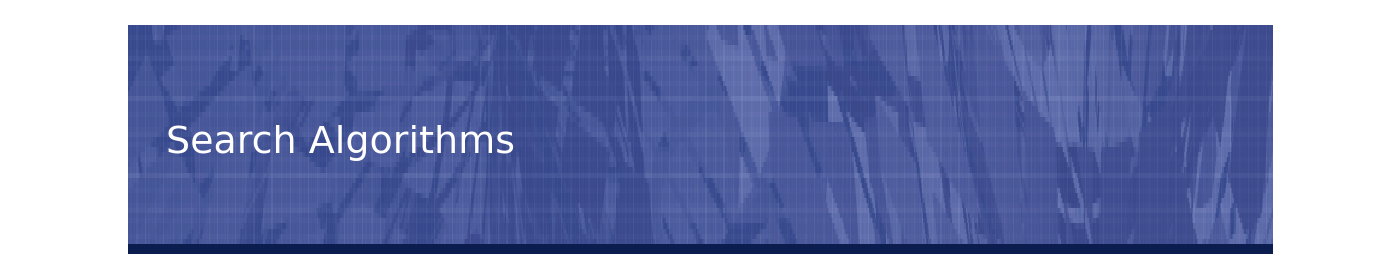
# 

## Presenter

Valeriu Ungureanu

## Data

DayName, Day MonthName Year

## Moldova State University

Normative Course

### Maсcивы Основные характеристики

Массив (англ. - array; в некоторых языках программирования также: таблица, ряд, матрица) — структура данных, хранящая набор значений (элементов массива), идентифицируемых по индексу или набору индексов, принимающих целые (или приводимые к целым) значения из некоторого заданного непрерывного диапазона.

Размерность массива — это количество индексов, необходимое для однозначной аддресации элемента в рамках массива.

Одномерный массив можно рассматривать как реализацию абстрактного типа данных вектор.

По количеству используемых индексов массивы делятся на: одномерные, двумерные, трёхмерные и т. д.

Форма или структура массива — сведения о количестве размерностей и длине (протяжённости) массива по каждой из размерностей может быть представлена одномерным массивом.

Особенностью массива как структуры данных (в отличие, например, от связного списка) является константная вычислительная сложность доступа к элементу массива по индексу.

Массив относится к структурам данных с произвольным доступом.

### Поиск в массиве Методы поиска

#### Типовые задачи поиска

1. найти наибольший (наименьший) элемент массива;
2. найти элемент массива, значение которого равно заданному значению.

В программировании поиск — одна из наиболее часто встречающихся задач невычислительного характера.

#### Решение задачи поиска

Компьютер не может сравнить разом весь ряд объектов. На каждом шаге он может сравнивать только два объекта. Поэтому в программе необходимо организовать последовательный просмотр элементов массива и сравнение значения очередного просматриваемого элемента с неким образцом.

#### Поиск наибольшего элемента

Рассмотрим подробно решение задач первого типа - нахождение наибольшего (наименьшего) элемента.

Представим себе одномерный массив в виде стопки карточек, на каждой из которых написано число. Тогда идея поиска наибольшего элемента массива может быть представлена следующим образом:

берется верхняя карточка (первый элемент массива), запоминается имеющееся на карточке число (можно записать его мелом на доске) как наибольшее из просмотренных; карточка убирается в сторону;

берется следующая карточка; сравниваются числа, записанные на карточке и на доске; если число на карточке больше, то стирается число, записанное на доске, и записывается там число, что на карточке; если же новое число не больше, то на доске не проводятся изменения; карточка убирается в сторону;

повторются действия, описанные в пункте 2, для всех оставшихся карточек в стопке.

В итоге на доске будет записано самое большое значение просмотренного массива.

Так как доступ к значению элемента массива осуществляется по его индексу, то при организации поиска наибольшего элемента в одномерном массиве правильнее искать его индекс.

```mathematica
a=RandomInteger[{-1000,1000},100]
```

{-982,620,661,474,-698,2,722,-398,-250,-367,-729,940,754,217,-260,-149,727,-510,-892,874,-916,-131,296,352,630,448,-699,-39,-629,-620,89,-984,-749,-860,695,37,506,605,-938,-58,-805,-588,649,339,-232,-308,-901,165,811,-600,-966,200,-608,577,-998,-223,-788,-424,956,-985,-692,363,71,337,-146,-877,-484,616,-80,-843,187,226,865,117,-509,982,-192,296,691,-756,397,181,-587,407,-277,-88,-796,980,76,-945,783,-723,-747,-204,788,-399,165,-444,664,-182}

```mathematica
max=a⟦1⟧;
For[i=2,i≤100,i++,
                  If[max<a⟦i⟧,max=a⟦i⟧]
  ];
max
```

#### Поиск элемента массива, равного заданному значению

Результатом решения задачи второго типа может быть:

n  — индекс элемента массива для которого  a[n] = x , где  x  — заданное число;

сообщение о том, что искомого элемента в массиве не обнаружено.

Алгоритм поиска в сформированном нами массиве может выглядеть так:

```mathematica
n=0;
s=-424;
For[i=1,i≤100,i++,
                  If[s==a⟦i⟧,n=i]
  ];

If[n==0,
     Print["В массиве нет элемента равного ",s],
     Print["Элемент с номером ",n," имеет искомое значение ",s]
]
```

Элемент с номером 58 имеет искомое значение -424

В этом коде последовательно просматриваются все элементы массива. Если в массиве несколько элементов, значения которых равны заданному числу, то программа найдет последний из них.

Во многих случаях требуется найти первый из элементов, имеющих соответствующее значение, и дальнейший просмотр массива прекратить. Для этой цели можно использовать следующие коды:

```mathematica
n=0;
s=-424;

For[i=1,i≤100,i++,
                  If[s==a⟦i⟧,n=i;Break[]]
  ];

If[n==0,
    Print["В массиве нет элемента равного ",s],
    Print["Элемент с номером ",n," имеет искомое значение ",s]
]
```

Элемент с номером 58 имеет искомое значение -424

```mathematica
i=1;
s=101;

While[s≠a⟦i⟧&&i< 100,i++];

If[s==a⟦i⟧,
     Print["Элемент с номером ",i," имеет искомое значение ",s],
     Print["В массиве нет элемента равного ",s]
]
```

В массиве нет элемента равного 101

Здесь выполнение алгоритма будет прервано в одном из двух случаев:

- в массиве найден первый из элементов, равный заданному;
- все элементы массива просмотрены.
 
Когда требуется определить количество элементов, удолетворяющих некоторому условию,   вводится переменная, значение которой увеличивается на единицу каждый раз, когда найден нужный элемент.

### Поиск в упорядоченном массиве Двоичный/бинарный поиск

#### Описание алгоритма двоичного поиска

Двоичный поиск эффективен в упорядоченном массиве.

l и r - левая и правая границы (индексы) отрезка массива, где находится нужный элемент.

m - средний элемент отрезка [l, r].

Если искомое значение меньше среднего элемента, делается переход к поиску в нижней/левой половине отрезка, где все элементы меньше только что проверенного, т.е.  значение r становится равной m – 1 и на следующей итерации исследуется левая половина массива.

Двоичный поиск - очень мощный метод т.к. в результате каждой проверки вдвое сужается область поиска.

Кроме поиска бывает нужно вставлять и удалять элементы. К сожалению, массив плохо приспособлен для выполнения таких операций.

#### Алгоритм двоичного поиска в языке Wolfram

```mathematica
Clear[a];
a=Sort@RandomInteger[{-1000,1000},100]
```

{-983,-972,-964,-960,-946,-894,-815,-801,-790,-759,-747,-742,-707,-693,-666,-662,-657,-624,-623,-608,-553,-544,-544,-539,-467,-454,-451,-444,-437,-422,-422,-417,-416,-403,-401,-362,-328,-324,-287,-282,-267,-266,-236,-230,-220,-216,-201,-144,-112,-108,-56,-54,-25,10,53,61,115,196,196,204,206,207,219,268,274,286,289,289,302,314,331,332,337,353,418,480,484,517,523,572,670,685,693,772,779,792,808,819,832,841,842,863,868,876,902,920,929,937,986,989}

```mathematica
s=989;
l=1;
r=Length[a];
Do[m=Floor[(l+r)/2];
     If[s<a⟦m⟧,
                           r=m-1,
                           If[s>a⟦m⟧,l=m+1,Break[]]
  ],
     Length[a]
]

If[s==a⟦m⟧, 
     Print["Элемент с номером ",m," имеет искомое значение ",s],
     Print["В массиве нет элемента равного ",s]
]
```

Элемент с номером 100 имеет искомое значение 989

#### Алгоритм двоичного поиска в C++:

int search(el e)
{
	int a=0, b=n-1;
	int result;
	while(a<b)
	{
		int i=(a+b)/2;
		if(ncomp++, (result=e.cmp(t[i]))>0)
		      a=i+1;
		else
		      if(result<0)
		             b=i;
             	                   else
			a=b=i;
	}
	return (ncomp++, e==t[a])? a : -1;
};

#### Сложность алгоритма двоичного поиска

Как определить сложность двоичного алгоритма в наихудшем случае?

Нетрудно заметить что наихудшим являтся случай когда после k итераций деления n на 2 получается значение ≤ 1, т. е. n/2^k≤ 1, или n≤ 2^k, или k ≥ ⌈log_2 n⌉.

```mathematica
Reduce[ {n≤ 2^k,n>0},k,Integers]
```

k∈ℤ&&k≥6

Сложность двоичного алгоритма: O(log_2 n).

Например, для массива из 100 элементов число итераций равно:

```mathematica
Log[2,1000000]//Ceiling
```

20

### Поиск в упорядоченном массиве Поиск интерполированием

#### Описание алгоритма

Поиск интерполированием эффективен в упорядоченном массиве большого размера.

Как и в алгоритме двоичного поиска переменные l и r содержат, соответственно, левую и правую границы отрезка массива, где находится нужный элемент. На каждой итерации исследуется средний элемент отрезка по формуле:
m=l+(s-a[l])(r-l)/(a[r]-a[l])
На каждой итерации проверяeтся если искомый элемент содержится в интервале [l, r].

#### Алгоритм в языке Wolfram

```mathematica
Clear[a];
a=Sort@RandomInteger[{-1000,1000},100]
```

{-992,-971,-969,-949,-910,-899,-877,-864,-856,-854,-854,-847,-843,-842,-818,-816,-812,-789,-782,-757,-701,-684,-663,-663,-648,-641,-634,-616,-593,-548,-518,-476,-457,-432,-413,-373,-371,-360,-342,-327,-308,-301,-255,-249,-236,-191,-174,-150,-146,-125,-108,-108,-90,-53,-15,5,12,14,15,25,25,67,80,85,88,92,99,147,213,220,224,286,317,350,390,413,445,449,460,474,489,533,556,641,714,732,759,777,849,851,853,871,885,894,935,947,954,963,971,973}

```mathematica
s=a⟦49⟧;
l=m=1;
r=Length[a];

While[l<r&&a⟦l⟧≤s≤a⟦r⟧,
           m=Ceiling[l+(s-a⟦l⟧)(r-l)/(a⟦r⟧-a⟦l⟧)];
                         If[s>a⟦m⟧,
                           l=m+1,
                           If[s<a⟦m⟧,r=m-1,Break[]];
                       ];
]

If[l==r,m=r];
If[s==a⟦m⟧, 
     Print["Элемент с номером ",m," имеет искомое значение ",s],
     Print["В массиве нет элемента равного ",s]
]
```

Элемент с номером 49 имеет искомое значение -146

#### Алгоритм в C++:

// C++ program to implement interpolation search 
#include<bits/stdc++.h> 
using namespace std; 
  
// If x is present in arr[0..n-1], then returns 
// index of it, else returns -1. 
int interpolationSearch(int arr[], int n, int x) 
{ 
    // Find indexes of two corners 
    int lo = 0, hi = (n - 1); 
  
    // Since array is sorted, an element present 
    // in array must be in range defined by corner 
    while (lo <= hi && x >= arr[lo] && x <= arr[hi]) 
    { 
        if (lo == hi) 
        { 
            if (arr[lo] == x) return lo; 
            return -1; 
        } 
        // Probing the position with keeping 
        // uniform distribution in mind. 
        int pos = lo + (((double)(hi - lo) / 
            (arr[hi] - arr[lo])) * (x - arr[lo])); 
  
        // Condition of target found 
        if (arr[pos] == x) 
            return pos; 
  
        // If x is larger, x is in upper part 
        if (arr[pos] < x) 
            lo = pos + 1; 
  
        // If x is smaller, x is in the lower part 
        else
            hi = pos - 1; 
    } 
    return -1; 
} 
  
// Driver Code 
int main() 
{ 
    // Array of items on which search will 
    // be conducted. 
    int arr[] = {10, 12, 13, 16, 18, 19, 20, 21, 
                 22, 23, 24, 33, 35, 42, 47}; 
    int n = sizeof(arr)/sizeof(arr[0]); 
  
    int x = 18; // Element to be searched 
    int index = interpolationSearch(arr, n, x); 
  
    // If element was found 
    if (index != -1) 
        cout << “Element found at index “ << index; 
    else
        cout << “Element not found.”; 
    return 0; 
}

#### Сложность алгоритма

Această metodă este eficientă în cazul în care n este foarte mare si valorile elementelor tabloului au o distribuţie uniformă în intervalul a[1],...,a[n]. Numărul de căutări în acest caz este de ordinul lg(lg n).

### Поиск в упорядоченном массиве Алгоритм Фибоначчи

#### Описание алгоритма Фибоначчи

Алгоритм Фибоначчи эффективен в упорядоченном массиве. По количеству операций в наихудшем случае он чуть, чуть, уступает двоичному поиску.

Алгоритм строится на основе чисел Фибоначчи, которые вычисляются по рекурентной формуле:

F_0=0;
F_1=1;
F_n=F_(n-1)+F_(n-2), n≥2.

В языке Wolfram существует встроенная функция Fibonacci[] для чисел Фибоначчи.

```mathematica
Table[Fibonacci[i],{i,15}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610}

Алгоритм похож на алгоритм двоичного поиска. Переменные l и r содержат, соответственно, левую и правую границы отрезка массива, где находится нужный элемент. Элемент m является внутренним элементом на отрезке поиска. Все три элемента являются последовательными числами Фибонначчи и они выбраны так что r является наименьшим числом Фибоначчи которое больше или равно n - длине массива.

На каждой итерации исследуется элемент масива с индексом l.

Пусть a[1...n] заданный массив а s искомый элемент.

1. Пусть r наименьшее число Фибоначчи которое больше или равно n. Пусть l и m предыдущие два числа Фибоначчи, а eliminated = 0 и означает количество исключенных элементов от начала масива.
2. Итеративно исследуется элемент масива с индексом l.
    Если a[l]=s, элемент найден и возвращается индекс l.
    Если a[l]<s, тройку Фибоначчи l, m и r, “спускаем” на два уровня вниз и  область поиска сужается почти на две третьи.
    Если a[l]>s, тройку Фибоначчи l, m и r, “спускаем” на один уровень вниз;
переменной eliminated присваиваем значение равное текущему индексу и  область поиска сужается чуть больше чем на треть.
3. Так как может остаться всего один элемент для сравнений, то он сравнивается с искомым значением. Если совпадают, то возвращается соответствуюший индекс.

В результате каждой проверки область поиска сужается не меньше чем на треть.

#### Алгоритм Фибоначчи в языке Wolfram

```mathematica
Clear[a];
a=Sort@RandomInteger[{-1000,1000},100]
```

{-981,-956,-911,-903,-902,-887,-852,-850,-830,-812,-795,-790,-788,-770,-759,-728,-670,-662,-648,-629,-571,-565,-562,-557,-557,-525,-516,-507,-503,-487,-459,-448,-443,-440,-390,-382,-366,-364,-345,-297,-274,-251,-206,-202,-196,-196,-191,-188,-183,-180,-177,-119,-58,-37,-35,-33,-25,-21,-17,-12,1,56,89,91,97,125,187,202,220,236,262,296,310,323,382,405,428,453,460,486,495,495,504,526,539,548,548,566,592,633,634,665,671,733,767,772,784,820,902,990}

```mathematica
n=Length[a];
s=990;

i=0;While[Fibonacci[i]<n,i++];
		l=Fibonacci[i-2];
		m=Fibonacci[i-1];
		r=Fibonacci[i];

eliminated=0;

While[r>1,
	i=Min[eliminated+l,n];
	If[a⟦i⟧<s,
	r=m;
	m=l;
	l=r-m;
	eliminated=i,
	If[a⟦i⟧>s,
		r=l;
		m=m-l;
		l=r-m,
	         Break[]
	]
       ]
]

If[s==a⟦i⟧, 
     Print["Элемент с номером ",i," имеет искомое значение ",s],
     Print["В массиве нет элемента равного ",s]
]
```

Элемент с номером 100 имеет искомое значение 990

#### Алгоритм Фибоначчи в C++

// C program for Fibonacci Search 
#include <stdio.h> 
  
// Utility function to find minimum of two elements 
int min(int x, int y) { return (x<=y)? x : y; } 
  
/* Returns index of x if present,  else returns -1 */
int fibMonaccianSearch(int arr[], int x, int n) 
{ 
    /* Initialize fibonacci numbers */
    int fibMMm2 = 0;   // (m-2)’th Fibonacci No. 
    int fibMMm1 = 1;   // (m-1)’th Fibonacci No. 
    int fibM = fibMMm2 + fibMMm1;  // m’th Fibonacci 
  
    /* fibM is going to store the smallest Fibonacci 
       Number greater than or equal to n */
    while (fibM < n) 
    { 
        fibMMm2 = fibMMm1; 
        fibMMm1 = fibM; 
        fibM  = fibMMm2 + fibMMm1; 
    } 
  
    // Marks the eliminated range from front 
    int offset = -1; 
  
    /* while there are elements to be inspected. Note that 
       we compare arr[fibMm2] with x. When fibM becomes 1, 
       fibMm2 becomes 0 */
    while (fibM > 1) 
    { 
        // Check if fibMm2 is a valid location 
        int i = min(offset+fibMMm2, n-1); 
  
        /* If x is greater than the value at index fibMm2, 
           cut the subarray array from offset to i */
        if (arr[i] < x) 
        { 
            fibM  = fibMMm1; 
            fibMMm1 = fibMMm2; 
            fibMMm2 = fibM - fibMMm1; 
            offset = i; 
        } 
  
        /* If x is greater than the value at index fibMm2, 
           cut the subarray after i+1  */
        else if (arr[i] > x) 
        { 
            fibM  = fibMMm2; 
            fibMMm1 = fibMMm1 - fibMMm2; 
            fibMMm2 = fibM - fibMMm1; 
        } 
  
        /* element found. return index */
        else return i; 
    } 
  
    /* comparing the last element with x */
    if(fibMMm1 && arr[offset+1]==x)return offset+1; 
  
    /*element not found. return -1 */
    return -1; 
} 
  
/* driver function */
int main(void) 
{ 
    int arr[] = {10, 22, 35, 40, 45, 50, 80, 82, 
                 85, 90, 100}; 
    int n = sizeof(arr)/sizeof(arr[0]); 
    int x = 85; 
    printf(“Found at index: %d”, 
            fibMonaccianSearch(arr, x, n)); 
    return 0; 
}

#### Сложность алгоритма Фибоначчи. Cравнение с другими алгоритмами

Как определить сложность алгоритма Фибоначчи в наихудшем случае?

Нетрудно заметить что наихудшим являтся случай когда после k итераций уменьшения игтервала на 1/3 получается значение ≤ 1, т. е. n(2/3)^к≤ 1,  или k ≥ ⌈log_(3/2)n⌉.

```mathematica
Reduce[ {n≤ (3/2)^k,n>0},k,Integers]
```

k∈ℤ&&k≥12

Последнее выражение и составляет сложность алгоритма Фибоначчи: O(log_(3/2)n).

Например, для массива из 100 элементов число итераций равно:

```mathematica
Log[3/2,100.]//Ceiling
```

12

Сравнение сложности алгоритмов поиска: последовательного, двоичного и Фибоначчи.

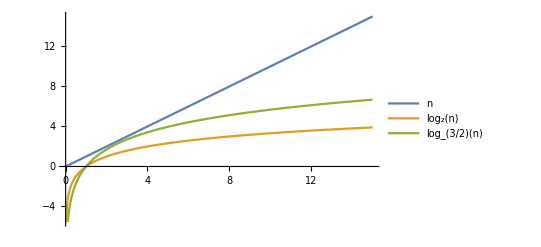

```mathematica
Plot[{n,Log[2,n],Log[3/2,n]},{n,0,15},PlotLegends->"Expressions"]
```